# Universal Quantum Computation: Demonstration

Here we provide a simple demonstration that any arbitrary unitary operation can be implemented by combining CNOT gate and single-qubit rotations.

TwoLevelDecomposition | returns a list of two-level unitary operators.
TwoLevelU | represents the two-level unitary operators.
GrayTwoLevelU | rewrites the two-level unitary operators in terms of CNOT and controlled-U gates.

Some functions conveniently used for the demonstration of universal quantum computation.

### Step 1. Decomposition into two-Level unitary operations

We first decompose the unitary operation into two-level unitary operations, that is, unitary operators acting only on a two-dimensional subspace.

Gray is a supplementary package and is not loaded by default when the Q3 App is loaded. You need to load it manually.

```mathematica
<<Q3`Gray`
```

```mathematica
Let[Qubit,S]
```

Consider a 2^n×2^n unitary matrix.

```mathematica
n=2;
mat=RandomUnitary[2^n];
mat//MatrixForm
```

(0.389087+0.543455 ⅈ | -0.38693-0.541707 ⅈ | -0.261118+0.0257278 ⅈ | 0.178684-0.0966078 ⅈ
0.0838575+0.453469 ⅈ | 0.0528813+0.428989 ⅈ | -0.349239+0.212027 ⅈ | -0.408331+0.516573 ⅈ
-0.405453-0.12518 ⅈ | -0.578345+0.02985 ⅈ | 0.000984296-0.0521667 ⅈ | 0.412514+0.558277 ⅈ
0.245447+0.316693 ⅈ | -0.120732+0.14163 ⅈ | 0.711495-0.505257 ⅈ | -0.1289+0.163402 ⅈ)

This is an explicit operator expression of the unitary transformation.

```mathematica
nn=Range[n];
SS=S[nn,None];
opU=ExpressionFor[mat,SS]
```

(0.0785131+0.27092 ⅈ)+(0.0515803+0.0825087 ⅈ) S_1^z S_2^z-(0.399722+0.549992 ⅈ) S_1^z S_2^+-(0.313819-0.479363 ⅈ) S_1^z S_2^-+(0.0736068-0.245423 ⅈ) S_1^+S_2^z+(0.178684-0.0966078 ⅈ) S_1^+S_2^+-(0.349239-0.212027 ⅈ) S_1^+S_2^--(0.142361+0.133405 ⅈ) S_1^-S_2^z-(0.578345-0.02985 ⅈ) S_1^-S_2^++(0.245447+0.316693 ⅈ) S_1^-S_2^-+(0.142471+0.215302 ⅈ) S_1^z-(0.334725-0.27115 ⅈ) S_1^+-(0.263093-0.00822544 ⅈ) S_1^-+(0.116523-0.0252757 ⅈ) S_2^z+(0.012792+0.00828464 ⅈ) S_2^++(0.397676-0.025894 ⅈ) S_2^-

Here is a two-level decomposition, where the results are in terms of TwoLevelUpaclet:Q3/ref/TwoLevelU.

```mathematica
mm=TwoLevelDecomposition[mat]
```

{TwoLevelU[{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.894224-0.44762 ⅈ}},{3,4},4],TwoLevelU[{{-0.694733-0.214492 ⅈ,-0.133182+0.6735 ⅈ},{0.133182+0.6735 ⅈ,-0.694733+0.214492 ⅈ}},{3,4},4],TwoLevelU[{{-0.112739-0.609649 ⅈ,0.784613},{-0.784613,-0.112739+0.609649 ⅈ}},{2,3},4],TwoLevelU[{{0.0404391-0.183505 ⅈ,0.519499-0.833554 ⅈ},{-0.519499-0.833554 ⅈ,0.0404391+0.183505 ⅈ}},{3,4},4],TwoLevelU[{{0.389087+0.543455 ⅈ,0.743819},{-0.743819,0.389087-0.543455 ⅈ}},{1,2},4],TwoLevelU[{{-0.520194-0.728278 ⅈ,0.446105},{-0.446105,-0.520194+0.728278 ⅈ}},{2,3},4],TwoLevelU[{{-0.786922+0.0775349 ⅈ,0.538495-0.291144 ⅈ},{-0.538495-0.291144 ⅈ,-0.786922-0.0775349 ⅈ}},{3,4},4]}

You can convert the above results to more human readable full matrix form by means of Matrixpaclet:Q3/ref/Matrix.

```mathematica
MatrixForm/@Matrix/@mm
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1.+0. ⅈ | 0
0 | 0 | 0 | 0.894224-0.44762 ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -0.694733-0.214492 ⅈ | -0.133182+0.6735 ⅈ
0 | 0 | 0.133182+0.6735 ⅈ | -0.694733+0.214492 ⅈ),(1 | 0 | 0 | 0
0 | -0.112739-0.609649 ⅈ | 0.784613 | 0
0 | -0.784613 | -0.112739+0.609649 ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0.0404391-0.183505 ⅈ | 0.519499-0.833554 ⅈ
0 | 0 | -0.519499-0.833554 ⅈ | 0.0404391+0.183505 ⅈ),(0.389087+0.543455 ⅈ | 0.743819 | 0 | 0
-0.743819 | 0.389087-0.543455 ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | -0.520194-0.728278 ⅈ | 0.446105 | 0
0 | -0.446105 | -0.520194+0.728278 ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -0.786922+0.0775349 ⅈ | 0.538495-0.291144 ⅈ
0 | 0 | -0.538495-0.291144 ⅈ | -0.786922-0.0775349 ⅈ)}

Check the decomposition with the original matrix.

```mathematica
new=Dot@@Matrix/@mm;
mat-new//Chop//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Step 2. Rewriting two-level unitary operators to elementary gates.

Now we rewrite each two-level unitary operator in terms of elementary gates, that is, in a combination of CNOT gates and one controlled-U gate.

GrayTwoLevelUpaclet:Q3/ref/GrayTwoLevelU does the job.

```mathematica
gates=Catenate[GrayTwoLevelU[#,S@nn]&/@mm]
```

{ControlledU[{S_1},(0.947112-0.22381 ⅈ)+(0.0528881+0.22381 ⅈ) S_2^z,Label→U],ControlledU[{S_1},(-0.694733+0. ⅈ)+(0.+0.6735 ⅈ) S_2^x-(0.+0.133182 ⅈ) S_2^y-(0.+0.214492 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(-0.112739+0. ⅈ)-(0.+0.784613 ⅈ) S_2^y+(0.+0.609649 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(0.0404391+0. ⅈ)-(0.+0.833554 ⅈ) S_2^x+(0.+0.519499 ⅈ) S_2^y-(0.+0.183505 ⅈ) S_2^z,Label→U],{S_1^x},ControlledU[{S_1},(0.389087+0. ⅈ)+(0.+0.743819 ⅈ) S_2^y+(0.+0.543455 ⅈ) S_2^z,Label→U],{S_1^x},CNOT[{S_2},{S_1}],ControlledU[{S_1},(-0.520194+0. ⅈ)-(0.+0.446105 ⅈ) S_2^y+(0.+0.728278 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(-0.786922+0. ⅈ)-(0.+0.291144 ⅈ) S_2^x+(0.+0.538495 ⅈ) S_2^y+(0.+0.0775349 ⅈ) S_2^z,Label→U]}

Here is a quantum circuit model of the decomposition. Here controlled-U gates are all labeled by the same character "U" but in fact they are different operators. Also do not forget to reverse the order of the elementary gates in the quantum circuit model.

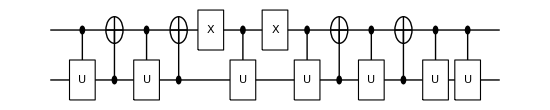

```mathematica
qc=QuantumCircuit[Reverse@gates]
```

```mathematica
new=ExpressionFor[qc]
```

(0.0785131+0.27092 ⅈ)-(0.125863-0.115491 ⅈ) S_1^x S_2^x+(0.14887-0.0739674 ⅈ) S_1^x S_2^y-(0.0343769+0.189414 ⅈ) S_1^x S_2^z+(0.057781+0.040586 ⅈ) S_1^y S_2^x-(0.337929-0.00544795 ⅈ) S_1^y S_2^y+(0.0560089+0.107984 ⅈ) S_1^y S_2^z-(0.356771+0.0353145 ⅈ) S_1^z S_2^x+(0.514677-0.0429517 ⅈ) S_1^z S_2^y+(0.0515803+0.0825087 ⅈ) S_1^z S_2^z-(0.298909-0.139688 ⅈ) S_1^x-(0.131463+0.0358159 ⅈ) S_1^y+(0.142471+0.215302 ⅈ) S_1^z+(0.205234-0.00880467 ⅈ) S_2^x-(0.0170893+0.192442 ⅈ) S_2^y+(0.116523-0.0252757 ⅈ) S_2^z

```mathematica
new-opU//Elaborate//Chop
```

0

Related Guides

Quisso Package Guide

Related Tutorials

Quisso: Quick Start

QuantumCircuit Usage Examples

Quantum Fourier Transform

Quantum Teleportation

Related Wolfram Education Group Courses

An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/

The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/